```mathematica
SetDirectory[NotebookDirectory[]]
<<"cryptolib2.wl"
```

/Users/marco/marco.live/DIDATTICA/CORSI/2025-2026/IN450/code/IN450-2025/src

```mathematica
X=StringDrop[Import["https://club.di.unimi.it/Cryptowars2020.zip","*"][[-2]],212];
```

```mathematica
X="0001 DTDRN FTIFA NPLOI WGLDR ETGOI SBOUI DTCRR LTSLE DPUGA UXIPP \\\\
0051 JTSHI GRAQT GRHHF MGODL LTMSO UWESA KHAUO ABOUI VPFUI UPIOM \\\\
0101 SGEHI FURDN UXAQO UFUHR LPNWO KTGXE FSOOI JTELG ADVHN AAFXR \\\\
0151 GGIGA YGAPA FIEOO JGEFH WHIGI WKAQT GSIYE FSIFA JAAPO JIEGI \\\\
0201 LGOLA FDSRP JPRHC SGLRI EEEUA LDRUO EPNRD AGOGO JAAQD GXNXN \\\\
0251 ETDHS EDTUA LIOFO KPNRN VTTWA ACPUO KPMDI FTIQR ABAFH WEEUA \\\\
0301 EDRYE FCELN XJRRR WTMDT LDDXO ERHHS AHAJG ADEUA KIIPA LDPUI \\\\
0351 EPSHD SROOE ARHHT SAQXA KXMKA XPTWO UWEOP GROLN YTGQO SSOUA \\\\
0401 VDRPI DXMDM WCEVA JEEUO LPNWO UDNFE KHOFH WBIEA KIIDF ACIUQ \\\\
0451 MPNWO ZDPUO ETSVO HXAFC APVLG WCEUO KPEUC MAEDP JDLHO JCAPE \\\\
0501 FIOHS HAEQD GGDHL KTCRL FDSWR GXPSO DXTRA YVRDD AGQXE KIOFH \\\\
0551 WKURL WTDDR NXSRL HJOOU EXLVE JKOYO KIRRQ MTLFH ADVLD WQBRP \\\\
0601 GHSRD AEAUO DTPDG SGELN HPRWE WSOSE JPDLN UWIRS LGOQE UWESO \\\\
0651 UDIRV ASIDD SXMSU LPRVO FDCKE IJAQT GXOSO KHOGA JIUWT GKIGO \\\\
0701 FDVRI KTNWI JTTHF JPISI MSEJN ATRRI UWEQO EXNDR UDNOA MSEPA \\\\
0751 HEAUE URHLO JXCRR VPRTU WARXG YXEUC ZTFXD AKOLE VTVRS LGIDV \\\\
";
```

0.0249664

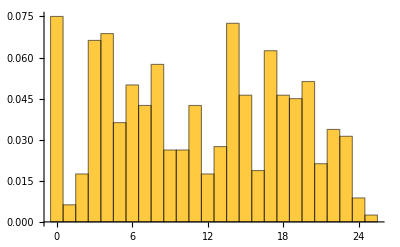

```mathematica
ciphertext=ToCode[X];
N@TruncatedCoincidenceIndex[ciphertext,50,150,7]
Histogram[ciphertext,26,"Probability"]
```

```mathematica
mguess=KasiskiTest[ciphertext,4]
```

5

```mathematica
blocks=Transpose@Partition[ciphertext,mguess];
Mean[ICs=N@Map[TruncatedCoincidenceIndex[#,50,160,7]&,blocks]]
(*naivekeyguess=Flatten@Map[Mod[ArgMaxFreq[Distribution[#],1]-mfita,26]
&,blocks];*)
ICs
```

0.0613522

{0.0470912,0.0679245,0.0658805,0.0472484,0.0786164}

```mathematica
blk=blocks[[5]]

candidates=Flatten@ArgMaxFreq[Distribution[blk],1]
Map[MutualIncidence[ITA,MessageShiftDecrypt[#,blk]]&,candidates]
N[Distribution[blk],3][[26]]
mfITA=ArgMaxFreq[Distribution[ITA],1][[1,1]]
Map[MutualIncidence[ITA,Mod[blk-#,26]]&,Flatten@Mod[ArgMaxFreq[blk,1]-mfITA,26]]
```

{13,0,8,17,8,8,17,4,0,15,8,19,5,11,14,0,14,8,8,12,8,13,14,17,14,4,8,6,13,17,0,0,14,7,8,19,4,0,14,8,0,15,2,8,0,14,3,14,3,13,18,0,14,13,0,14,8,17,7,0,4,13,17,19,14,18,6,0,0,8,3,4,19,0,0,14,15,13,14,0,8,12,0,14,14,4,7,0,5,16,14,14,14,2,6,14,2,15,14,4,18,3,11,11,17,14,0,3,4,7,11,17,11,20,4,14,16,7,3,15,3,14,6,13,4,4,13,18,4,14,21,3,20,14,4,19,14,0,19,14,8,8,5,8,13,8,14,17,0,0,4,14,17,20,6,2,3,4,18,21}

{14}

{0.0444315}

0

8

{0.0385124,0.0374886}

```mathematica
MutualIncidence[ITA,Mod[blocks[[1]]-18,26]]
```

```mathematica
Length[blocks[[1]]]
```

```mathematica
?ArgMaxFreq
```

```mathematica
Length[blocks]
MutualIncidence[ITA,MessageShiftDecrypt[0,blocks[[5]]]]
```

```mathematica
?ArgMaxFreq
```

```mathematica
(*
kguess=Flatten@ArgMaxFreq[Distribution[blk],4]
Map[MutualIncidence[ITA,MessageShiftDecrypt[#,blk]]&,kguess]
*)
```

```mathematica
?MutualIncidence
```

```mathematica
keyguess=ParallelMap[BestKeyITA,blocks];
FromCode@keyguess
plaintext=FromCode@VigenereDec[keyguess,ciphertext]
```

```mathematica
StringTake[StringDrop[X,111],200]
blk=blocks[[5]]
N@CoincidenceIndex[blk]
4/7N@CoincidenceIndex[blk]
```

```mathematica
dctx=Transpose@{Range[0,25],Distribution[blk]};
sortedkeys=Map[({Mod[#[[1]]-mfITA,26],#[[2]]})&,Reverse@SortBy[dctx,Last]];
G1=ListLinePlot@Table[MutualIncidence[ITA,MessageShiftDecrypt[key=sortedkeys[[i,1]],blk]],{i,0,25}];
G2=ListLinePlot[Table[4/7N@CoincidenceIndex[blk],{i,0,25}],PlotStyle->Orange];
```

```mathematica
Show[G1,G2]
```

```mathematica
N@CoincidenceIndex[blk]2/3
```

```mathematica
TruncatedCoincidenceIndex[ciphertext,60,160,7]
Map[TruncatedCoincidenceIndex[#,60,160,7]&,blocks]
```